## Definimos una lista de artículos que vamos a investigar y buscamos una serie de informaciones para evaluarlos en un sentido general

```mathematica
writers={"Carolina Maria de Jesus","Clarice Lispector","Gabriela Mistral","Júlia Lopes de Almeida","Machado de Assis","Lima Barreto (escritor)","Mário de Andrade","Jorge Luis Borges"}
```

{Carolina Maria de Jesus,Clarice Lispector,Gabriela Mistral,Júlia Lopes de Almeida,Machado de Assis,Lima Barreto (escritor),Mário de Andrade,Jorge Luis Borges}

```mathematica
{"Carolina Maria de Jesus","Clarice Lispector","Gabriela Mistral","Júlia Lopes de Almeida","Machado de Assis","Lima Barreto","Mário de Andrade","Jorge Luis Borges"}
```

{Carolina Maria de Jesus,Clarice Lispector,Gabriela Mistral,Júlia Lopes de Almeida,Machado de Assis,Lima Barreto,Mário de Andrade,Jorge Luis Borges}

Definition of Wikipedia API for different languages :

```mathematica
Clear[WikiAPI]
WikiAPI["Portuguese"]="https://pt.wikipedia.org/w/api.php";
WikiAPI["Spanish"]="https://es.wikipedia.org/w/api.php";
WikiAPI["English"]="https://en.wikipedia.org/w/api.php";
WikiAPI["French"]="https://fr.wikipedia.org/w/api.php";
```

Let’s look for some statistics of these authors and make charts with them to have a sense of their visibility/invisibility.

```mathematica
Clear[WikiName,WikiPageID,DigitStringQ,WikiPageQ,WikiLanguages]
(* WikiName returns the canonic name of an article in a given language *)
WikiName[art_String,lang_String]:=WikipediaData[art,"Title",Language->lang];
WikiName[arts_List,lang_String]:=Join@@Map[WikipediaData[#,"Title",Language->lang]&,Partition[arts,UpTo[50]]];
(* WikiPageID returns the page ID of an article in a given language *)
WikiPageID[art_String,lang_String]:=WikipediaData[art,"PageID",Language->lang];
WikiPageID[arts_List,lang_String]:=Join@@Map[WikipediaData[#,"PageID",Language->lang]&,Partition[arts,UpTo[50]]];
(* DigitStringQ returns True or False, depending of whether a string is solely composed of digits 0...9 *)
DigitStringQ[str_]:=If[StringQ[str],StringMatchQ[str,DigitCharacter..],False];
(* WikiPageQ returns True or False, depending of whether a specific article exists in a given language *)
WikiPageQ[art_String,lang_String]:=DigitStringQ[WikipediaData[art,"PageID",Language->lang]];
(* WikiLanguages returns a list of languages for a specific article *)
WikiLanguages[art_String,lang_String]:=WikipediaData[art,"LanguagesList",Language->lang];
WikiLanguages[arts_List,lang_String]:=Join@@Map[WikipediaData[#,"LanguagesList",Language->lang]&,Partition[arts,UpTo[50]]];
```

```mathematica
Clear[WikiLanguageChart]
WikiLanguageChart[arts_List,lang_String]:=Module[{data,counts},
data=WikiLanguages[arts,lang];
counts=Map[Length,data];
BarChart[counts,ChartLegends->arts,ChartStyle->"Pastel",AxesLabel->{"Writer's Wikipedia article","number of languages"},ImageSize->Large,LabelingFunction->Above]
]
```

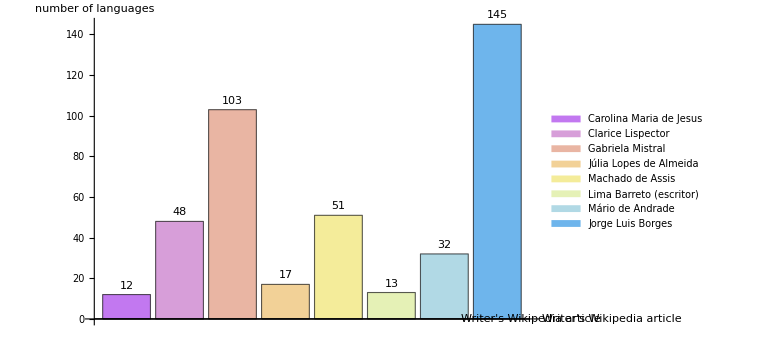

```mathematica
WikiLanguageChart[writers,"Portuguese"]
```

The first think we notice is that the two most prominent in terms of global circulation are not lusophone but spanish-speaking. It is surprising that Clarice Lispector and Machado de Assis, the two most prominent in the lusohpone world, are way behind them. The two least circulating are black writers, Carolina Maria de Jesus and Lima Barretoin which we see intersectional meanings involving class, race and gender.

#### Now, we will make a chart with the sizes of the different pages in Portuguese

```mathematica
Clear[WikiPageSize]
(* This function returns the lenght of an article in a given language *)
WikiPageSize[articles_List,lang_String]:=Module[{arts,data,titles,pagesize},
arts=StringRiffle[articles,"|"];
data=URLExecute[WikiAPI[lang],{"action"->"query","format"->"json","formatversion"->2,"titles"->arts,"prop"->"info"}];
titles="title"/.("pages"/.("query"/.data));
pagesize=Map[ToExpression,"length"/.("pages"/.("query"/.data))];
If[Not[SameQ[Union[titles],Union[articles]]],Print["Warning (LG): Probable API spelling mismatch."]];
articles/.Inner[Rule,titles,pagesize,List]
]/;Length[articles]<=40;
WikiPageSize[art_String,lang_String]:=WikiPageSize[{art},lang][[1]];
WikiPageSize[articles_List,lang_String]:=Join@@Map[WikiPageSize[#,lang]&,Partition[articles,UpTo[40]]];
```

NOTE WikiPageSize is giving back the page sizes according to the pageid number (from lowest to highest) . We need to modify the code so that it coincides with the original list . 
NOTE 2 I changed code. We need to be sure that “title” as returned by the API coincides with what we gave it in articles parameter

```mathematica
WikiPageSize[{"Mário de Andrade","Carolina Maria de Jesus","Carolina Maria de Jesus"},"Portuguese"]
```

{batchcomplete→True,query→{pages→{{pageid→1291,ns→0,title→Mário de Andrade,contentmodel→wikitext,pagelanguage→pt,pagelanguagehtmlcode→pt,pagelanguagedir→ltr,touched→2026-02-07T02:27:47Z,lastrevid→71679376,length→54946},{pageid→1428545,ns→0,title→Carolina Maria de Jesus,contentmodel→wikitext,pagelanguage→pt,pagelanguagehtmlcode→pt,pagelanguagedir→ltr,touched→2026-02-07T02:32:54Z,lastrevid→71607363,length→63317}}}}

{Mário de Andrade,Carolina Maria de Jesus}

{54946,63317,63317}

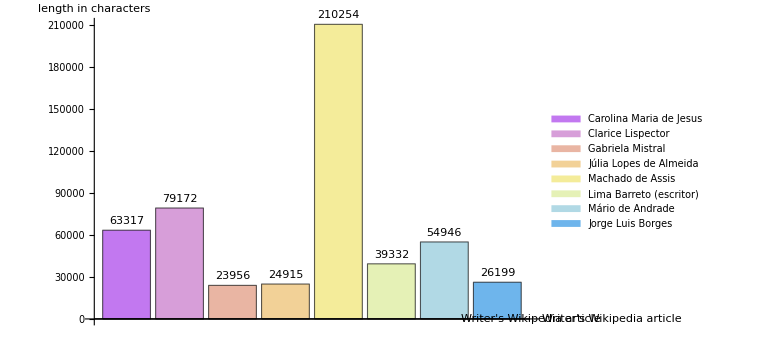

```mathematica
BarChart[WikiPageSize[writers,"Portuguese"],ChartLegends->writers,ChartStyle->"Pastel",AxesLabel->{"Writer's Wikipedia article","length in characters"},ImageSize->Large,LabelingFunction->Above]
```

#### Lo que vemos en la tabla es una interesante medida de la atención dada a dif. intelectuales en la Wikipedia lusófona. Por un lado, dos intelectuales fundamentales del mundo hispanico y de gran circulacion mundial como JLB y GM tienen artículos breves, mostrando poco interés, seguidos por dos intelectuales importantes del siglo XIX e inicios del XX en Brasil, como Lima Barreto y Julia Lopes de Ameida, que denota un interés moderado en la figura de ellos. Es interesante notar que tanto LB como Jorge Luis Borges foram indicados como artigos com poucas referências, e que os editores deveriam inserir mais (https://pt.wikipedia.org/wiki/Wikip%C3%A9dia:Verificabilidade), enquanto GM foi marcado como esboço, ou seja que também deve ser expandido, o que chama a atenção porque é um artigo de extensão considerável (https://pt.wikipedia.org/wiki/Wikip%C3%A9dia:Esbo%C3%A7o). Já os artigos de Mário de Andrade, CLarice Lispector e Carolina Maria de Jesus estão em outro grupo, de artigos mais extensos e mais completos. Inclusive, o artigo de MA é considerado “bom” pela ferramenta automatizada da plataforma (https://pt.wikipedia.org/wiki/Wikip%C3%A9dia:Artigos_bons), enquanto os da CL e CMJ não. Existem de fato poucos artigos considerados dessa forma sobre mulheres, e em um mapeamento geral, consideramos que não é claro o critério que diferencia esses dos mencionados (Berta Ribeiro, Anna Mae Barbosa, Elvy Kalep, com artigos menores, com menos referências que os anteriores.) O artigo sobre CL possui mais de 100 referências e mais extensão que muitos desses, por exemplo. Já o artigo de Machado de Assis é considerado destacado na plataforma https://pt.wikipedia.org/wiki/Wikip%C3%A9dia:Artigos_destacados), pela sua qualidade. https://pt.wikipedia.org/wiki/Categoria:!Artigos_bons_sobre_mulheres, https://pt.wikipedia.org/wiki/Categoria:!Artigos_destacados_sobre_mulheres. Un estudio queda pendiente sobre cuáles artículos son destacados sobre mujeres y por qué. O da CL, o da CMJ são mais extensos e possuem mais referências que o do MA, no entanto, não são considerados “bons”. Ou seja que na plataforma, número de referências ou extensão não são necessariamento índices de que um artigo seja considerado bom. Sim são índices - para nós - de artigos que concentram trabalho dos editores.

API based function that returns the list of editors (contributors) of a given entry in a given language. Es importante aclarar que esta función ofrece la lista de editores registrados de una página de wikipedia, y no los editores que no se registraron. 
Esto nos da una idea de cuánta atención recibió cada uno de estos artículos.

```mathematica
Clear[ExtractKeyFromList]
(* This function returns all the values of a given key in a list *)
ExtractKeyFromList[list_List,key_String]:=Map[key/.#&,list];
ExtractKeyFromList[list_List,keys_List]:=Map[keys/.#&,list];
```

```mathematica
Clear[WikiEditors,WikiEditorsNumber]
WikiEditors[art_String,lang_String]:=Module[{data,cont,stop,editors},
cont="";
editors={};
Label["loop"];
data=URLExecute[WikiAPI[lang],Join[{"action"->"query","format"->"json","formatversion"->2,"titles"->art,"prop"->"contributors","pclimit"->"max"},If[cont=="",{},{"pccontinue"->cont}]]];
editors=Join[editors,ExtractKeyFromList["contributors"/.("pages"/.("query"/.data)),"name"][[1]]];
stop=TrueQ[("batchcomplete"/.data)];
If[Not[stop],cont="pccontinue"/.("continue"/.data);Goto["loop"]];
editors
]
WikiEditors[articles_List,lang_String]:=Map[WikiEditors[#,lang]&,articles];
WikiEditorsNumber[articles_List,lang_String]:=Map[Length[WikiEditors[#,lang]]&,articles];
```

```mathematica
WikiEditorsNumber[{"Mário de Andrade","Clarice Lispector"},"Portuguese"]
```

{245,331}

```mathematica
Length[WikiEditors["Carolina Maria de Jesus","Portuguese"]]
```

128

```mathematica
Union[WikiEditors["Carolina Maria de Jesus","Portuguese"]]//TableForm
```

```mathematica
WikiEditorsNumber[writers,"Portuguese"]
```

{126,331,81,58,396,175,245,168}

Una tabla que muestra la cantidad de editores registrados de los artículos.

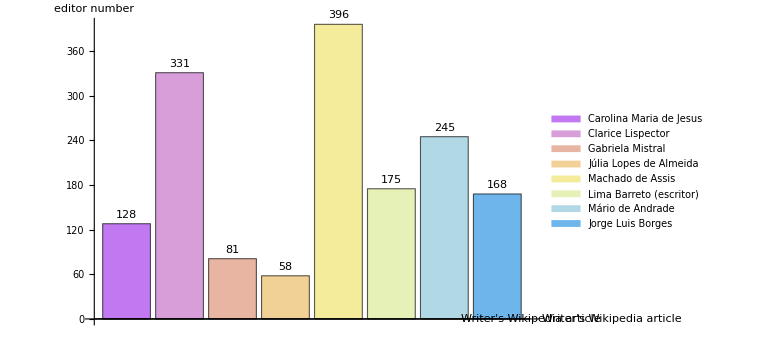

```mathematica
BarChart[WikiEditorsNumber[writers,"Portuguese"],ChartLegends->writers,ChartStyle->"Pastel",AxesLabel->{"Writer's Wikipedia article","editor number"},ImageSize->Large,LabelingFunction->Above]
```

Notamos que os escritores homens possuem maior quantidade de editores registrados que as mulheres, inclusive entre os homens que menos edições possuem.  
A média de editores registrados nos artigos de mulheres é 149, enquanto a média de editores registrados nos artigos dos homens é de 246, um número considerávelmente maior.

```mathematica
Clear[arts,X,Y]
arts=writers;
X=Map[Length[WikiEditors[#,"Portuguese"]]&,arts]
Y=Map[WikiPageSize[#,"Portuguese"]&,arts]
```

{128,331,81,58,396,175,245,168}

{65245,79172,23956,24915,213585,39308,54810,26199}

```mathematica
{X,Y}
Transpose[%]
```

{{128,331,81,58,396,175,245,168},{65245,79172,23956,24915,213585,39308,54810,26199}}

{{128,65245},{331,79172},{81,23956},{58,24915},{396,213585},{175,39308},{245,54810},{168,26199}}

Una tabla que muestra la cantidad de editores con relación a la extensión (si la incluyo, necesitaría labels)

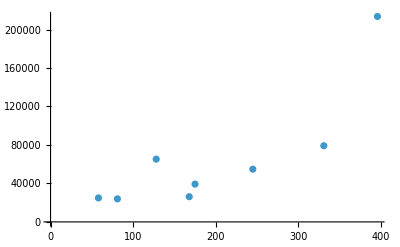

```mathematica
ListPlot[Transpose[{X,Y}]]
```

Lo que vemos acá como cosa interesante es: los que más editores tienen son CL y MA, y también tienen artículo más largo. Luego viene MA, en tercer lugar, a pesar de no tener un artículo tan largo. En cuarto y quinto están Lima Barreto y Jorge Luis Borges. En sexto está CMJ, a pesar de no tener tantos editores, tiene menos de la mitad, tiene un artículo considerable (o sea que sus editores escriben mucho). En el caso de GM, tiene pocos editores, 51 para la extensión del artículo, lo que se explica porque seguramente es una traducción (por eso recibe la categoría de esbozo). Es el caso de JLA, tiene 81 editores y un artículo relativamente corto. 
Lo que vemos es que los artículos sobre mujeres tienen menos editores que los de los hombres, concentran menos cantidad de editores y de interés por parte de la comunidad wikipedista, y esto es consistente teniendo en cuenta el lugar que ocupan en el campo cultural. (CL tiene más que MAndrade, pero también es una autora mucho más reconocida a nivel mundial, un bestseller editorial. )

```mathematica
Correlation[X,Y]//N
```

0.819937

Creamos la función Wikirevisions, que da una serie de propiedades de la historia de ediciones de un artículo. Por ejemplo, ofrece el ID de la revisión, el momento, el usuario, el tamaño final del artículo después de las revisiones, los comentarios hechos sobre la revisión. Pedimos, entre esas, el ID del revisor (incluye cuentas no registradas), el nombre de usuario, el momento, el comentario y el tamaño.
Del tamaño final, restamos el tamaño inicial, antes de la revisión, para ver si se trató de una adición o una sustracción de texto. 
Cómo hago para ver si hay pocos usuarios que eliminan mucho en hombres y mujeres? Será que son muchos o pocos los eliminadores? Será que hay algunos usuarios comunes que son los grandes eliminadores?

```mathematica
Clear[WikiRevisions,WikiTotalEditors,WikiTotalEditorsNumber,WikiTotalRevisionsNumber]
WikiRevisions[art_String,lang_String]:=Module[{data,cont,stop,revisions,sizes,prevsizes,diff},
cont="";
revisions={};
Label["loop"];
data=URLExecute[WikiAPI[lang],Join[{"action"->"query","format"->"json","formatversion"->2,"titles"->art,"prop"->"revisions","rvprop"->"ids|timestamp|user|userid|size|flags|comment|tags","rvlimit"->"max"},If[cont=="",{},{"rvcontinue"->cont}]]];
(*Print[data];*)
revisions=Join[revisions,ExtractKeyFromList["revisions"/.("pages"/.("query"/.data)),{"revid","user","userid","timestamp","comment","size"}][[1]]];
stop=TrueQ[("batchcomplete"/.data)];
If[Not[stop],cont="rvcontinue"/.("continue"/.data);Goto["loop"]];
sizes=revisions[[All,-1]];
prevsizes=Append[Drop[sizes,1],0];
diff=sizes-prevsizes;
Transpose[Append[Transpose[revisions],diff]]
];
WikiTotalEditors[art_String,lang_String]:=Module[{revs,eds},
revs=WikiRevisions[art,lang];
eds=revs[[All,2]];
Union[eds]
];
WikiTotalEditorsNumber[art_String,lang_String]:=Length[WikiTotalEditors[art,lang]];
WikiTotalEditorsNumber[arts_List,lang_String]:=Map[WikiTotalEditorsNumber[#,lang]&,arts];
WikiTotalRevisionsNumber[art_String,lang_String]:=Length[WikiRevisions[art,lang]];
WikiTotalRevisionsNumber[arts_List,lang_String]:=Map[WikiTotalRevisionsNumber[#,lang]&,arts]
```

```mathematica
WikiTotalRevisionsNumber["Mário de Andrade","Portuguese"]
```

966

```mathematica
WikiTotalRevisionsNumber[writers,"Portuguese"]
```

{434,1518,215,116,2076,855,966,447}

```mathematica
WikiTotalEditorsNumber[writers,"Portuguese"]
```

{197,719,114,72,793,449,520,271}

```mathematica
WikiTotalEditorsNumber["Mário de Andrade","Portuguese"]
```

520

Una tabla que muestra la cantidad de ediciones en los artículos seleccionados (incluye eliminaciones).

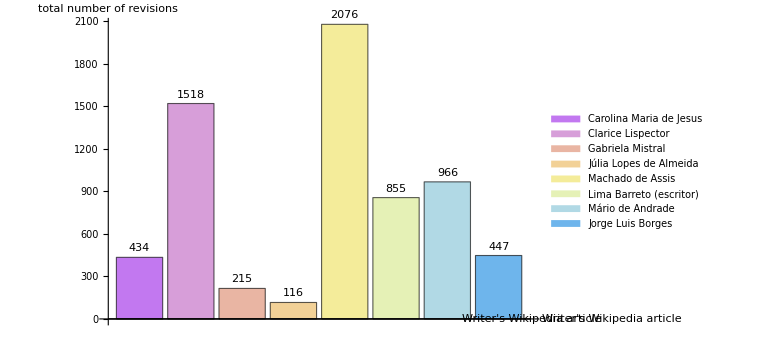

```mathematica
BarChart[WikiTotalRevisionsNumber[writers,"Portuguese"],ChartLegends->writers,ChartStyle->"Pastel",AxesLabel->{"Writer's Wikipedia article","total number of revisions"},ImageSize->Large,LabelingFunction->Above]
```

Interesante: lo que vemos es que a extensión parecida, similar posición en el campo intelectual, el número total de ediciones es mucho más grande en todos los casos de hombres en comparación con mujeres escritoras. Las mujeres tienen una media de 570, mientras que los hombres tienen una media de casi el doble, con 1086 ediciones. Los hombres nutren casi el doble de atenci.08ón y trabajo que las mujeres (sin considerar si son de pocos o muchos caracteres, o si son eliminaciones o agregados). Eso es lo que vemos en el histograma, las mujeres reciben mucha menos atención de los editores que los hombres. 
En esta tabla, no importa si pocos editores agregan mucho contenido, o si eliminan.
Si tomamos a GM y JLB, vemos que los editores de JLB son casi el doble de GM. Si tomamos a LB y CMJ, también son casi el doble. Tomando a JJLA, todos superan ese número, (talvez deberíamos cambiar a Cecília Meirelles?). Agregar un apartado sobre cómo fue hecho el recorte. Figuras del Siglo XIX y XX, sobre todo de la primera y segunda mitad del siglo, hasta los años 80, consolidados. Equilibrio en terminos de género, buscamos la posibilidad de comparar figuras de hombres y mujeres relativamente equivalentes por su posición, su notoriedad, qué tomamos en cuenta para evaluar su lugar en la circulación literaria y el campo intelectual.

Una tabla que muestra todos los revisores, registrados y no registrados, automatizados o humanos.

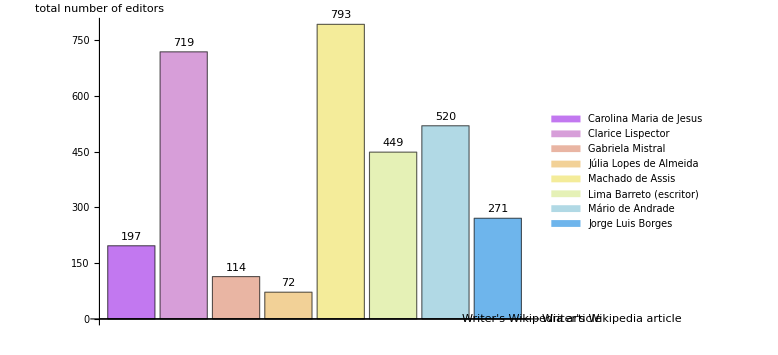

```mathematica
BarChart[WikiTotalEditorsNumber[writers,"Portuguese"],ChartLegends->writers,ChartStyle->"Pastel",AxesLabel->{"Writer's Wikipedia article","total number of editors"},ImageSize->Large,LabelingFunction->Above]
```

Acá lo que vemos es que el número total de editores de las mujeres es considerablemente más grande que el de los hombres. La única excepción es la de CL, es interesante notar que el número de editores es casi igual que el de MA, casi el doble fueron editores no registrados (esta regla cuando cambió? Será que hasta una cierta época no era obligatorio tener editores registrados). La media de editores de las mujeres es de 275, mientras que la de los hombres es 508, solo un poco menos del doble. Eso nos habla de un trabajo mucho más nutrido en torno de los hombres, en el paisaje discursivo de la plataforma, que en los discursos sobre las mujeres. 
Ahora bien, si quisieramos analizar cómo se distribuye ese trabajo de edición, podemos hacer histogramas.

```mathematica
data1=WikiRevisions["Gabriela Mistral","Portuguese"][[All,-1]];
data2=WikiRevisions["Jorge Luis Borges","Portuguese"][[All,-1]];
```

```mathematica
PairedHistogram[data1,data2 ,{-300,300,50},ChartLegends->{"Revisiones en el articulo de Gabriela Mistral","Revisiones en el de Jorge Luis Borges"},ChartStyle->{54,None,None},AxesLabel->{"","Characters"}]
```

-Graphics-

Lo que vemos en este histograma comparativo, es que la mayor cantidad de ediciones son pequeñas, de menos de 100 caracteres, así como la mayor cantidad de eliminaciones. Lo que vemos también es que a pesar de que la cantidad total de ediciones en el artículo de JLB es mucho mayor al de GM, casi el doble, la distribución es similar, o sea que en ambos casos hay gran cantidad de ediciones menores. Además vemos también una distribución similar de borrado en ambos casos, que refuta nuestra hipótesis de que habría más borrado en el caso de las mujeres. Con esto, podemos construir hipótesis sobre que si el artículo de GM es de una extensión parecida al de JLB es probablemente porque hubo algunas pocas ediciones de muchos caracteres (talvez una traducción, y esto explica que sea considerado un esbozo). 
Es importante notar entonces que: los artículos sobre mujeres concentran menos atención de los editores y menos trabajo, y no se trata de más borrado.  (En este punto no estamos considerando los artículos eliminados)

```mathematica
data2=WikiRevisions["Lima Barreto (escritor)","Portuguese"][[All,-1]];
```

```mathematica
data1=WikiRevisions["Carolina Maria de Jesus","Portuguese"][[All,-1]];
```

```mathematica
PairedHistogram[data1,data2 ,{-500,500,50},ChartLegends->{"Revisiones en el articulo de CMJ","Revisiones en el de LB"},ChartStyle->{54,None,None},AxesLabel->{"","Characters"}]
```

-Graphics-

Nuevamente, el artículo de LB concentra más ediciones. Sin embargo, ambas tienen una distribución similar, con bastantes ediciones pequeñas, de pocos caracteres, algo de borrado, de pocos caracteres también, y una larga cola de menos cantidad de ediciones de una cantidad de texto más considerable.

```mathematica
data2=WikiRevisions["Mário de Andrade","Portuguese"][[All,-1]];
```

```mathematica
data1=WikiRevisions["Carolina Maria de Jesus","Portuguese"][[All,-1]];
```

```mathematica
PairedHistogram[data1,data2 ,{-1000,1000,200},ChartLegends->{"Revisiones en el articulo de CMJ","Revisiones en el de MA"},ChartStyle->{54,None,None},AxesLabel->{"","Characters"}]
```

-Graphics-

```mathematica
data2=WikiRevisions["Machado de Assis","Portuguese"][[All,-1]];
```

```mathematica
data1=WikiRevisions["Clarice Lispector","Portuguese"][[All,-1]];
```

```mathematica
PairedHistogram[data1,data2 ,{-500,500,100},ChartLegends->{"Revisiones en el articulo de CL","Revisiones en el de MA"},ChartStyle->{54,None,None},AxesLabel->{"","Characters"}]
```

-Graphics-

Una misma distribución se repite en todos los casos.

```mathematica
WikiRevisions["Carolina Maria de Jesus","Portuguese"][[All,{2,-1}]]
```

```mathematica
Length[WikiRevisions["Carolina Maria de Jesus","Portuguese"][[All,1]]]
```

434

API based function that returns the list of categories to which a given entry in a given language belongs:

```mathematica
Clear[WikiCategories]
WikiCategories[art_String,lang_String]:=Module[{data,cont,stop,categs},
cont="";
categs={};
Label["loop"];
data=URLExecute[WikiAPI[lang],Join[{"action"->"query","format"->"json","formatversion"->2,"titles"->art,"prop"->"categories","cllimit"->"max"},If[cont=="",{},{"clcontinue"->cont}]]];
categs=Join[categs,ExtractKeyFromList["categories"/.("pages"/.("query"/.data)),"title"][[1]]];
stop=TrueQ[("batchcomplete"/.data)];
If[Not[stop],cont="clcontinue"/.("continue"/.data);Goto["loop"]];
categs
]
```

Un gráfico de barras con las categorías. Poder graficar con una lista de artículos cuantas categorías tiene cada uno.

```mathematica
WikiCategories[]
```

A Mathematica function using WikipediaData that computes the historical number of visits of a selection of articles?

```mathematica
Clear[WikiVisits]
WikiVisits[art_String,lang_String]:=Total[WikipediaData[art,"MonthlyPageHits",Language->lang]]
```

```mathematica
WikiVisits["Cecilia Grierson","Spanish"]
```

991249

```mathematica
Map[WikiVisits["Julieta Lanteri","Portuguese"]
```

747158

```mathematica
WikipediaData["Julieta Lanteri","MonthlyPageHits",Language->"Portuguese"]
```

TimeSeries[…]

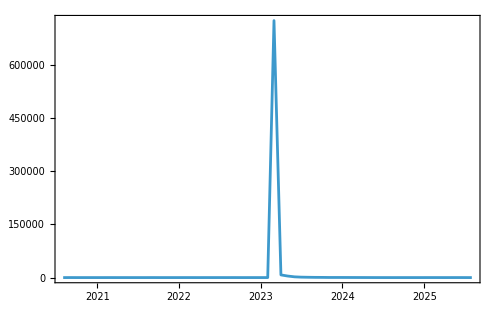

```mathematica
DateListPlot[%,PlotRange->Full,ImageSize->500]
```

```mathematica
Clear[f,list1]
f[article_]:={WikipediaData[article,"MonthlyPageHits",Language->"Portuguese"]}
list1=Map[f,list2];
list2=writers
```

{Carolina Maria de Jesus,Clarice Lispector,Gabriela Mistral,Júlia Lopes de Almeida,Machado de Assis,Lima Barreto (escritor),Mário de Andrade,Jorge Luis Borges}

```mathematica
DateListPlot[list1,PlotLegends->list2,PlotRange->All]
```

DateListPlot::ldata: {{{«1»}}} is not a valid dataset or list of datasets.

DateListPlot[{{{TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…]}}},PlotLegends→{Carolina Maria de Jesus,Clarice Lispector,Gabriela Mistral,Júlia Lopes de Almeida,Machado de Assis,Lima Barreto (escritor),Mário de Andrade,Jorge Luis Borges},PlotRange→All]

```mathematica
Export[path<>"tablavisitas.png",%]
```

Quiero una tabla de visitas totales de un grupo de artículos. Cuál tuvo más visitas totales. 
Hay alguna relación entre visitas totales, ediciones, número de editores, extensión, categorías?
Hay alguna casualidad? Es igual para las mujeres essa correlación entre medidas?
En todos los casos más editores y más ediciones es un artículo más extenso? 
Medidas del borrado pueden ser si cuando aumentan los editores disminuye la extensión de un artículo.  
Será que más visitas, se correlacionan con más borrado en el art. de las mujeres?